# N-Channel Square Well Model

NPM

## Setup

For background, see the “CoupledSqrWellV4.nb and *V5.nb” files as well as the original version of this file.  Here, I will set up a streamlined version of the code.

At the two-channel level, we have:

(-ℏ^2/(2μ)∂^2/(∂r^2)+V_1(r)+(ℏ^2 L(L+1))/(2μ r^2) | V_12
V_12 | -ℏ^2/(2μ)∂^2/(∂r^2)+V_2(r)+(ℏ^2 L(L+1))/(2μ r^2))( ψ_1
 ψ_2)=E (ψ_1
ψ_2)

Choose:

V_1(r)={-D_1
0         for  r<r_0
for r>r_0

V_2(r)={E_2^th-D_2
E_2^th      for  r<r_0
for r>r_0

We wish to measure length in units of r_0, and energy in units of ℏ^2/(2μ r_0^2), so we multiply through by r_0^2, and redefine r→ r/r_0:

(-∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(-D_1-E)+(L(L+1))/r^2 | (2μ r_0^2)/ℏ^2 V_12
(2μ r_0^2)/ℏ^2 V_12* | -∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(E_2^th-D_2-E)-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)=0

(-∂^2/(∂r^2)-(2μ r_0^2)/ℏ^2E+(L(L+1))/r^2 | 0
0 | -∂^2/(∂r^2)-(2μ r_0^2)/ℏ^2E-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)+(2μ r_0^2)/ℏ^2(-D_1 | V_12
V_12* | E_2^th-D_2)(ψ_1^I
ψ_2^I)=0

Now rescale all energies to be in units of ℏ^2/2μ r_0^2.  (effectively setting ℏ^2/2μ r_0^2→1

(-∂^2/(∂r^2)-E+(L(L+1))/r^2 | 0
0 | -∂^2/(∂r^2)-E-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)+(-D_1 | V_12
V_12* | E_2^th-D_2)(ψ_1^I
ψ_2^I)=0

((H_0-E)1+V)ψ=0

Solutions of just the diagonal operator are:

```mathematica
f[L_,k_,r_]=√(π/2 k r)BesselJ[L+1/2,k r];
```

```mathematica
df[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselJ[L+1/2,k r],r]];
```

```mathematica
g[L_,k_,r_]=√(π/2 k r)BesselY[L+1/2,k r];
```

```mathematica
dg[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselY[L+1/2,k r],r]];
```

I’ll multiply the decaying function by a constant to rescale it for the strongly closed channels.

```mathematica
gb[L_,κ_,r_]=√(2/π κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0.9;
```

```mathematica
dgb[L_,κ_,r_]=Simplify[D[gb[L,κ,r],r]];
```

```mathematica
fb[L_,κ_,r_]=√(2/π κ r)BesselI[L+1/2,k r];
```

```mathematica
dfb[L_,κ_,r_]=Simplify[D[√(2/π κ r)BesselI[L+1/2,k r],r]];
```

Now the constant matrix:

V=(-D_1 | V_12
V_12* | E_2^th-D_2)

can be diagonalized as:

Λ=(λ_1^2 | 0
0 | λ_2^2)

by an orthogonal transformation

Λ=UᵀV U ⇒ V=U Λ Uᵀ

Then

((H_0-E)1+U Λ Uᵀ)ψ=0

We can hit this from the left with Uᵀ and thus since it clearly commutes with 1 we write (using U^T U=1):

((H_0-E)1+Λ) Uᵀψ=0

((H_0-E)1+Λ) ϕ=0

where we define

ϕ=U^T ψ ⇒ψ=U ϕ

ϕ satisfies a diagonal equation (E=k^2)

(-∂^2/(∂r^2)+(L(L+1))/r^2 | 0
0 | -∂^2/(∂r^2)-(L(L+1))/r^2)(ϕ_1
ϕ_2)-((k^2-λ_1^2) | 0
0 | (k^2-λ_2^2))(ϕ_1
ϕ_2)=0

ψ=U ϕ

means

ψ_i=∑_α U_iα ϕ_α(r)

It helps perhaps to remember that this is really

ψ_i=∑_α U_iα∑_β δ_αβ ϕ_α(r)

However, we require the appropriate linear combination that matches smoothly onto the exterior solutions.  To obtain this, we construct a more general solution in the interior.  Let

Φ_iα=U_iα ϕ_α(r)

and now construct:

ψ_i=∑_α b_α Φ_iα

Note that the b_α are coefficients that only depend on α and therefore can’t be adjusted to give different amplitudes in the open-closed channels.  They only allow different superpositions of the functions in a given channel that are all regular at the origin, namely ϕ_α=f_α=√(π/2 k_α r)J_(L+1/2)(k_α r), where  k_α=√(k^2-λ_α^2).

Meanwhile the row index of U_iα carries information about the relative amplitudes in each channel.  It seems in a sense that for our purpose, the column index of U is irrelevant, since the dependence on α will be modified by the multiplication by b_α which still need to be determined anyhow.

To determine the solutions, we demand that the interior wave functions and their derivatives match smoothly onto the exterior solutions:

∑_α b_α Φ_iα={a_i g_b(r)
c_i f(k_i r)-s_i g(k_i r) i∈closed channels
i∈open channels

along with an additional equation for the open channel setting the c→1.  This is setup as a system of linear equations:

(Φ_11 | ⋯ | Φ_(1N) | -g_1 | 0 | 0 | 0 | 0
(∂Φ_11)/(∂r) | ⋯ | (∂Φ_(1N))/(∂r) | -(∂g_1)/(∂r) | 0 | 0 | 0 | 0
⋮ | ⋱ | ⋮ | 0 | ⋱ | 0 | 0 | 0
Φ_(N-1,1) | ⋯ | Φ_(N-1,N) | 0 | 0 | -g_(N-1) | 0 | 0
(∂Φ_(N-1,1))/(∂r) | ⋯ | (∂Φ_(N-1,N))/(∂r) | 0 | 0 | -(∂g_(N-1))/(∂r) | 0 | 0
Φ_N1 | ⋯ | Φ_NN | 0 | 0 | 0 | -f_o | g_o
(∂Φ_N1)/(∂r) | ⋯ | (∂Φ_NN)/(∂r) | 0 | 0 | 0 | -(∂f_o)/(∂r) | (∂g_o)/(∂r)
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)(b_1
⋮
b_N
a_1
⋮
a_(N-1)
c
s)=(0
0
⋮
0
0
0
0
1)

I’ve moved to Chris’s notation where the open channel is the last one and the first N-1 channels are closed.

```mathematica
SetupPotentialTriDiag[NumChan_,D0_,ϵ1_,γ_]:=
Module[{i,j,ϵthresh,Λvals,U,V},
(*ϵthresh=Table[ϵ1 (i-1),{i,1,NumChan}];*)
ϵthresh=Table[If[i==NumChan,0,i ϵ1],{i,1,NumChan}];
V=Table[If[i==j,-D0+i ϵ1-i ϵ1(KroneckerDelta[i,NumChan]),(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ],{i,1,NumChan},{j,1,NumChan}];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
{Λvals,U,ϵthresh,V}
]
```

```mathematica
SetupPotentialOpenClosed[NumChan_,D0_,ϵ1_,γ_]:=
Module[{i,j,ϵthresh,Λvals,U,V},
(*ϵthresh=Table[ϵ1 (i-1),{i,1,NumChan}];*)
ϵthresh=Table[If[i==NumChan,0,ϵ1],{i,1,NumChan}];
V=Table[0,{i,1,NumChan},{j,1,NumChan}];
Do[V[[i,i]]=-D0+0.5(i),{i,1,NumChan-1}];
V[[NumChan,NumChan]]=-D0-100.0;
Do[V[[i,NumChan]]=γ;V[[NumChan,i]]=γ,{i,1,NumChan-1}];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
{Λvals,U,ϵthresh,V}
]
```

```mathematica
NCHAN=3;D0=100.0;ϵ1=50.0;γ=2;NumOpen=1;L=0;rmatch=1.0;
{Λ,U,ϵth,V}=SetupPotentialOpenClosed[NCHAN,D0,ϵ1,γ];MatrixForm[V]
```

(-99.5 | 0 | 2
0 | -99. | 2
2 | 2 | -200.)

```mathematica
ϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,f[L,√(Energy-λsqr),r],fb[L,√(λsqr-Energy),r]];
dϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,df[L,√(Energy-λsqr),r],dfb[L,√(λsqr-Energy),r]];
```

```mathematica
MakeΦMat[NumChan_,L_,Λ_,U_,Energy_,r_]:=Module[
{Φ,dΦ,i,j},
Φ=Table[U[[i,j]]ϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
dΦ=Table[U[[i,j]]dϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
{Φ,dΦ}
]
```

```mathematica
ϵ=0.01;{Φ,dΦ}=MakeΦMat[NCHAN,L,Λ,U,ϵ,1];
MatrixForm[Simplify[Φ]]
MatrixForm[Simplify[dΦ]]
```

(-0.0198763 | -0.520001 | 0.0392021
-0.019778 | 0.0411193 | 0.498221
0.999574 | -0.00952651 | 0.0106375)

(0.00228503 | -8.48084 | 0.675713
0.00227372 | 0.670626 | 8.58765
-0.114913 | -0.15537 | 0.183355)

```mathematica
Dimensions[dΦ]
```

{3,3}

```mathematica
SetupABMat[NumChan_,NumOpen_,ϵthresh_,Φ_,dΦ_,L_,r_,Energy_]:=
Module[{i,j,SizeAB,κc,ko,NumClosed,Amat,Bmat,ABmat,bvec},
SizeAB=2 NumChan+1;Bmat=Table[0,{i,1,2 NumChan}];
NumClosed=NumChan-NumOpen;
(*Closed Channels Interior*)
Do[
Bmat[[2 i-1]]=Φ[[i]];
Bmat[[2 i]]=dΦ[[i]];,
{i,1,NumClosed}
];
(*Open Channel Interior*)
Bmat[[2 NumChan-1]]=Φ[[NumChan]];Bmat[[2 NumChan]]=dΦ[[NumChan]];

(*Closed Channels Exterior*)
Amat=Table[0,{i,2 NumChan},{j,NumChan+1}];
Do[Do[κc=√(ϵthresh[[i]]-Energy);Amat[[2 i-1,j]]=-gb[L,√(ϵthresh[[i]]-Energy),r]KroneckerDelta[i,j];
  Amat[[2 i,j]]=-dgb[L,√(ϵthresh[[i]]-Energy),r] KroneckerDelta[i,j];,{i,NumClosed}];,{j,NumClosed}];

(*Open Channel Exterior*)
ko=√(Energy-ϵthresh[[NumChan]]);
Amat[[2 NumChan-1,NumChan]]=f[L,ko,r];
Amat[[2 NumChan-1,NumChan+1]]=-g[L,ko,r];
Amat[[2 NumChan,NumChan]]=df[L,ko,r];
Amat[[2 NumChan,NumChan+1]]=-dg[L,ko,r];

(*Putting it all together*)

ABmat=Table[0,{i,SizeAB},{j,SizeAB}];
Do[If[j≤NumChan,ABmat[[i,j]]=Bmat[[i,j]]];
ABmat[[i,NumChan+j]]=-Amat[[i,j]];
,{i,2NumChan},{j,NumChan+1}];
(* Pick the open channel amplitude to be 1 *)
ABmat[[SizeAB,NumChan+NumClosed+1]]=1; 
bvec=Table[0,{i,SizeAB}];bvec[[SizeAB]]=1;

{ABmat,bvec}
]
```

```mathematica
SetupABMatNew[NumChan_,NumOpen_,ϵthresh_,Φ_,dΦ_,L_,r_,Energy_]:=
Module[{i,j,SizeAB,κc,ko,NumClosed,ABmat,bvec},
SizeAB=2 NumChan+1;
NumClosed=NumChan-NumOpen;
ABmat=Table[0,{i,1,SizeAB},{j,1,SizeAB}];
(*Closed Channels Interior*)

Do[
ABmat[[2 i-1,1;;NumChan]]=Φ[[i]];
ABmat[[2 i,1;;NumChan]]=dΦ[[i]];,
{i,1,NumClosed}
];
(*Open Channel Interior*)
ABmat[[2 NumChan-1,1;;NumChan]]=Φ[[NumChan]];ABmat[[2 NumChan,1;;NumChan]]=dΦ[[NumChan]];

(*Closed Channels Exterior*)
Do[
κc=√(ϵthresh[[i]]-Energy);ABmat[[2i-1,NumChan+i]]=-gb[L,√(ϵthresh[[i]]-Energy),r];
ABmat[[2 i,NumChan+i]]=-dgb[L,√(ϵthresh[[i]]-Energy),r];,
{i,1,NumClosed}];

(*Open Channel Exterior*)
ko=√(Energy-ϵthresh[[NumChan]]);
ABmat[[2 NumChan-1,NumChan+NumClosed+1]]=f[L,ko,r];
ABmat[[2 NumChan-1,NumChan+NumClosed+2]]=-g[L,ko,r];
ABmat[[2 NumChan,NumChan+NumClosed+1]]=df[L,ko,r];
ABmat[[2 NumChan,NumChan+NumClosed+2]]=-dg[L,ko,r];

(* Pick the open channel amplitude to be 1 *)
ABmat[[SizeAB,NumChan+NumClosed+1]]=1; 
bvec=Table[0,{i,SizeAB}];
bvec[[SizeAB]]=1;

{ABmat,bvec}
]
```

```mathematica
{AB,b}=SetupABMatNew[NCHAN,NumOpen,ϵth,Φ,dΦ,0,1,0.01];
```

```mathematica
MatrixForm[AB]
```

(-0.0198763 | -0.520001 | 0.0392021 | -0.493104 | 0 | 0 | 0
0.00228503 | -8.48084 | 0.675713 | 3.48642 | 0 | 0 | 0
-0.019778 | 0.0411193 | 0.498221 | 0 | -0.493104 | 0 | 0
0.00227372 | 0.670626 | 8.58765 | 0 | 3.48642 | 0 | 0
0.999574 | -0.00952651 | 0.0106375 | 0 | 0 | 0.0998334 | 0.995004
-0.114913 | -0.15537 | 0.183355 | 0 | 0 | 0.0995004 | -0.00998334
0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
sols=LinearSolve[AB,b]
```

{0.994785,-0.010362,0.0121226,-0.0282074,-0.0285157,1.,-1.09992}

```mathematica
Length[sols]
```

7

```mathematica
SolutionData[NumChan_,NumOpen_,ϵthresh_,sols_,L_,r_,Energy_]:=Module[
{ascat,sigma,aclose,aLsqr,norm,δOverπ,coef,σ,i,j,δ,SizeAB,tandel},

SizeAB=2NumChan+1;
tandel=sols[[SizeAB]]/sols[[SizeAB-1]];
ascat=-tandel/√Energy;
norm=1/(√(sols[[SizeAB-1]]^2+sols[[SizeAB]]^2));
δ=ArcTan[tandel];
δOverπ=δ/π;
aclose=sols[[NumChan+1;;2NumChan-1]];
coef=sols[[1;;NumChan]];
σ=(4π Sin[δ]^2)/Energy;
aLsqr=Sin[δ]^2;
{ascat,δOverπ,aLsqr,norm,aclose,coef}]
SolutionData[NCHAN,1,ϵth,sols,0,1,0.01]
```

{10.9992,-0.265134,0.547474,0.672701,{-0.0282074,-0.0285157},{0.994785,-0.010362,0.0121226}}

### Looping over parameters and energy

Using the functions defined above, we should now be able to loop over potential parameters and energy.  The first step is to define the potential, and transformation to dressed states:

```mathematica
NCHAN=3;D0=100.0;ϵ1=50.0;γ=2.0;NumOpen=1;L=0;rmatch=1.0;
{Λ,U,ϵth,V}=SetupPotentialTriDiag[NCHAN,D0,ϵ1,γ];
```

Next, set construct the interior solution basis.  If we wish to do this and loop over energy, then we need a loop over the following body of 
code:

```mathematica
Energy=0.01;
{Φ,dΦ}=MakeΦMat[NCHAN,L,Λ,U,Energy,rmatch];
{AB,b}=SetupABMatNew[NCHAN,NumOpen,ϵth,Φ,dΦ,0,rmatch,Energy];
sols=LinearSolve[AB,b];
SolutionData[NCHAN,1,ϵth,sols,0,1,0.01]
```

{-(10. (2.44954×10^-17 k Cosh[1. k]+1.73515×10^-13 Sinh[1. k]))/(-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k]),ArcTan[(1. (2.44954×10^-17 k Cosh[1. k]+1.73515×10^-13 Sinh[1. k]))/(-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k])]/π,(1. (2.44954×10^-17 k Cosh[1. k]+1.73515×10^-13 Sinh[1. k])^2)/((1+(1. (2.44954×10^-17 k Cosh[1. k]+1.73515×10^-13 Sinh[1. k])^2)/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k])^2)) (-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k])^2),1/(√(1.+(1. (2.44954×10^-17 k Cosh[1. k]+1.73515×10^-13 Sinh[1. k])^2)/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k])^2))),{(1. (-2.38311×10^-34 k^3 Cosh[1. k]^3-4.202×10^-30 k^2 Cosh[1. k]^2 Sinh[1. k]-1.85171×10^-26 k Cosh[1. k] Sinh[1. k]^2+5.04342×10^-26 Sinh[1. k]^3))/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k]) (4.46212×10^-14 k Cosh[1. k]+4.46389×10^-13 Sinh[1. k]) (1. k Cosh[1. k]+8817.57 Sinh[1. k])),(1. (-3.31749×10^-33 k^2 Cosh[1. k]^2-2.92012×10^-29 k Cosh[1. k] Sinh[1. k]+4.50076×10^-28 Sinh[1. k]^2))/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k]) (4.46212×10^-14 k Cosh[1. k]+4.46389×10^-13 Sinh[1. k]))},{(1. (-1.12329×10^-31 k^3 Cosh[1. k]^3-1.98206×10^-27 k^2 Cosh[1. k]^2 Sinh[1. k]-8.75332×10^-24 k Cosh[1. k] Sinh[1. k]^2-8.72818×10^-23 Sinh[1. k]^3))/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k]) (4.46212×10^-14 k Cosh[1. k]+4.46389×10^-13 Sinh[1. k]) (1. k Cosh[1. k]+8817.57 Sinh[1. k])),(1. (-2.33683×10^-34 k^3 Cosh[1. k]^3-4.123×10^-30 k^2 Cosh[1. k]^2 Sinh[1. k]-1.82035×10^-26 k Cosh[1. k] Sinh[1. k]^2-1.53458×10^-25 Sinh[1. k]^3))/((-2.57905×10^-16 k Cosh[1. k]-1.85076×10^-12 Sinh[1. k]) (4.46212×10^-14 k Cosh[1. k]+4.46389×10^-13 Sinh[1. k]) (1. k Cosh[1. k]+8817.57 Sinh[1. k])),(1. (6.58126×10^-24 √k Csch[1. k]+1.49276×10^-27 k^(3/2) Coth[1. k] Csch[1. k]+8.4647×10^-32 k^(5/2) Coth[1. k]^2 Csch[1. k]+7.58432×10^-48 k^(7/2) Coth[1. k]^3 Csch[1. k]))/((-1.85076×10^-12-2.57905×10^-16 k Coth[1. k]) (4.46389×10^-13+4.46212×10^-14 k Coth[1. k]) (8817.57+1. k Coth[1. k]))}}

```mathematica
{Λ,U,ϵth,V}=SetupPotentialTriDiag[NCHAN,D0,ϵ1,γ];
RunEnergyLoop[NumChan_,NumOpen_,L_,rmatch_,Λ_,U_,ϵth_,Energy_]:=Module[
{Φ,dΦ,AB,b,sols,data},
{Φ,dΦ}=MakeΦMat[NumChan,L,Λ,U,Energy,rmatch];
{AB,b}=SetupABMatNew[NumChan,NumOpen,ϵth,Φ,dΦ,L,rmatch,Energy];
sols=LinearSolve[AB,b];
data=SolutionData[NumChan,NumOpen,ϵth,sols,L,rmatch,Energy];
data
]
```

```mathematica
dataArray=Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data[[n]]},{n,1,3}],{ϵ,0.0001,ϵth[[1]],ϵth[[1]]/10000.0}];
```

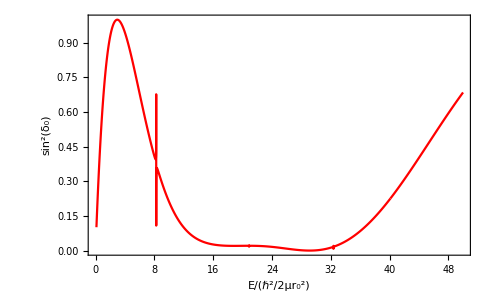

```mathematica
ptest=ListPlot[Transpose[dataArray][[3]],Joined->True,Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"}]
```

### Test the position of the resonances using the open-closed couplings

```mathematica
NCHAN=20;D0=2000.0;ϵ1=500.0;γ=10.0;NumOpen=1;L=0;rmatch=1.0;
{Λ,U,ϵth,V}=SetupPotentialOpenClosed[NCHAN,D0,ϵ1,γ];
dataArray=Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data[[n]]},{n,1,3}],{ϵ,0.0001,ϵth[[1]],ϵth[[1]]/10000.0}];
```

$Aborted

```mathematica
ptest=ListPlot[Transpose[dataArray][[3]],Joined->True,Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"}];
```

```mathematica
TEQ0=√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)];
Depths=Table[ϵth[[ichan]]-V[[ichan,ichan]],{ichan,1,NCHAN-1}];
NumSearch=1000;
egrid=Table[Table[e,{e,-Depths[[ichan]],-0.0001,Depths[[ichan]]/NumSearch}],{ichan,1,NCHAN-1}];
Bgrid=Table[Table[{egrid[[ichan,i]],TEQ0/.{ϵ->egrid[[ichan,i]],v0->Depths[[ichan]]}},{i,1,NumSearch}],{ichan,1,NCHAN-1}];
rootguess=Table[Table[0,50],{ichan,1,NCHAN-1}];
Do[rn=1;Do[If[ Bgrid[[ichan,i,2]]Bgrid[[ichan,i-1,2]]<0,rootguess[[ichan,rn]]=Bgrid[[ichan,i,1]];rn+=1;],{i,2,NumSearch}],{ichan,1,NCHAN-1}];
Do[rootguess[[ichan]]=rootguess[[ichan,1;;rn-1]],{ichan,1,NCHAN-1}];
roots=rootguess;
Do[Do[roots[[ichan,i]]=ϵ/.FindRoot[TEQ0==0/.v0->Depths[[ichan]],{ϵ,rootguess[[ichan,i]]}],{i,1,rn-1}],{ichan,1,NCHAN-1}];
poles=Table[Table[{{roots[[ichan,i]]+ϵth[[ichan]],1},{roots[[ichan,i]]+ϵth[[ichan]],1.2}},{i,1,rn-1}],{ichan,1,NCHAN-1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
graphpoles=Table[Line[poles[[n]]],{n,1,NCHAN-1}];
MatrixForm[V]
ϵth
```

(-1999. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | -1998. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | -1997. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | -1996. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | -1995. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | -1994. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | -1993. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1992. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1991. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1990. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1989. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1988. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1987. | 0 | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1986. | 0 | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1985. | 0 | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1984. | 0 | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1983. | 0 | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1982. | 0 | 10.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1981. | 10.
10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | 10. | -1980.)

{500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,0}

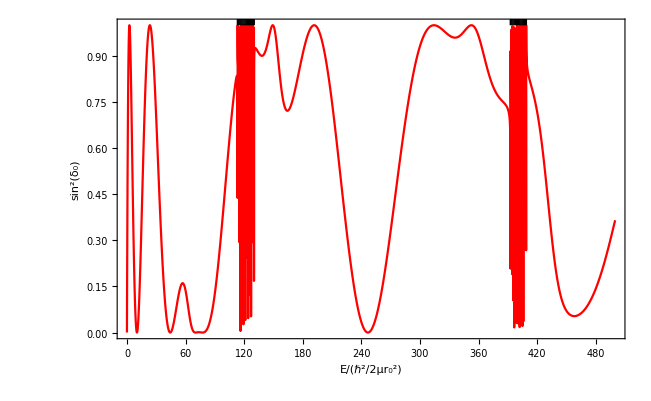

```mathematica
Show[ptest,Epilog->graphpoles]
```

Neat!  This looks like it could be a possible avenue for placing a large density of states at the collision threshold.  So what potential depths correspond to energies at the collision threshold?  The depths are V_i+ϵ_th(i), and we need a binding of ϵ_th, so search for energies -ϵ_th(i)

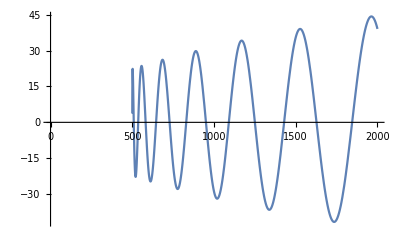

```mathematica
Plot[TEQ0/.ϵ->-ϵth[[1]],{v0,0,2000.0}];
```

```mathematica
FindRoot[TEQ0/.{ϵ->-ϵth[[1]]},{v0,1000.0}]
```

{v0→950.783}

Let’s try it again, this time placing a large density of states near threshold.

```mathematica
NCHAN=25;
ϵ1=500.0;γ=1.0;NumOpen=1;L=0;rmatch=1.0;
TotalDepthofClosedChannel=v0/.FindRoot[TEQ0/.{ϵ->-ϵ1},{v0,2000.0}];
{Λ,U,ϵth,V}=SetupPotentialOpenClosed[NCHAN,TotalDepthofClosedChannel-ϵ1,ϵ1,γ];
dataArray=Table[data=RunEnergyLoop[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ];Table[{ϵ,data[[n]]},{n,1,3}],{ϵ,0.0001,ϵth[[1]]/50,ϵth[[1]]/50/10000.0}];
```

```mathematica
ptest=ListPlot[Transpose[dataArray][[3]],Joined->True,Frame->True,PlotStyle->Red,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"}];
```

```mathematica
TEQ0=√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)];
Depths=Table[ϵth[[ichan]]-V[[ichan,ichan]],{ichan,1,NCHAN-1}];
NumSearch=1000;
egrid=Table[Table[e,{e,-Depths[[ichan]],-0.0001,Depths[[ichan]]/NumSearch}],{ichan,1,NCHAN-1}];
Bgrid=Table[Table[{egrid[[ichan,i]],TEQ0/.{ϵ->egrid[[ichan,i]],v0->Depths[[ichan]]}},{i,1,NumSearch}],{ichan,1,NCHAN-1}];
rootguess=Table[Table[0,50],{ichan,1,NCHAN-1}];
Do[rn=1;Do[If[ Bgrid[[ichan,i,2]]Bgrid[[ichan,i-1,2]]<0,rootguess[[ichan,rn]]=Bgrid[[ichan,i,1]];rn+=1;],{i,2,NumSearch}],{ichan,1,NCHAN-1}];
Do[rootguess[[ichan]]=rootguess[[ichan,1;;rn-1]],{ichan,1,NCHAN-1}];
roots=rootguess;
Do[Do[roots[[ichan,i]]=ϵ/.FindRoot[TEQ0==0/.v0->Depths[[ichan]],{ϵ,rootguess[[ichan,i]]}],{i,1,rn-1}],{ichan,1,NCHAN-1}];
poles=Table[Table[{{roots[[ichan,i]]+ϵth[[ichan]],1},{roots[[ichan,i]]+ϵth[[ichan]],1.2}},{i,1,rn-1}],{ichan,1,NCHAN-1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
graphpoles=Table[Line[poles[[n]]],{n,1,NCHAN-1}];
MatrixForm[V]
ϵth
```

(-1582.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | -1581.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | -1581.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | -1580.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | -1580.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | -1579.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | -1579.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1578.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1578.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1577.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1577.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1576.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1576.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1575.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1575.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1574.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1574.11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1573.61 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1573.11 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1572.61 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1572.11 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1571.61 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1571.11 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1570.61 | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | -1682.61)

{500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,500.,0}

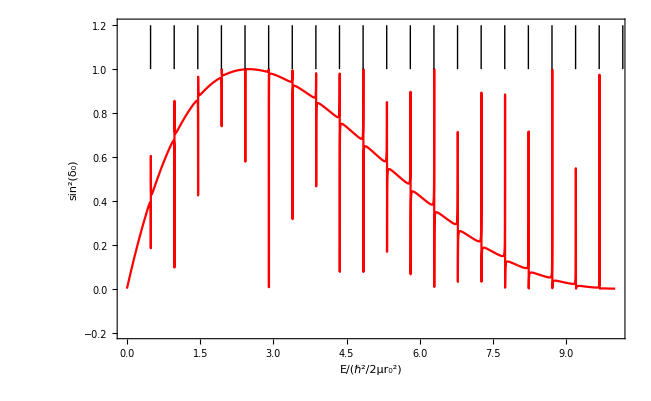

```mathematica
Show[ptest,Epilog->graphpoles,PlotRange->{{0.0,ϵth[[1]]/50},{-0.2,1.2}}]
```

Cool!  A high density of states right at threshold, for a fraction of the cost.  What happens when we crank up the coupling?

## 1-channel square well

As a preliminary to the multichannel case, we will need to solve the single channel case to understand where the bound states are with respect to the threshold.  This will help us interpret the two-channel resonances, at least in the weak coupling regime.  Inside the well of range r_0, the radial wavefunction R(r) satisfies:

(-ℏ^2/(2μ)1/r^2∂/(∂r)r^2∂/(∂r)+(-V_0-E)+(L(L+1))/r^2) R(r)=0

We let ψ(r)=r R(r)

(-ℏ^2/(2μ)∂^2/(∂r^2)+(-V_0-E)+(L(L+1))/r^2)ψ(r)=0

(∂^2/(∂r^2)+(2μ)/ℏ^2(E+V_0)-(L(L+1))/r^2) ψ(r)=0

Let ϵ=(2μ r_0^2 E)/ℏ^2 and v_0=(2μ r_0^2 V_0)/ℏ^2.  Also RESCALE r→r/r_0.  Then

(∂^2/(∂r^2)+ϵ+v_0-(L(L+1))/r^2)ψ(r)=0

When v_0=0, with x=√ϵ r the solutions are:

```mathematica
DSolve[ψ''[x]+1ψ[x]-(L(L+1))/x^2 ψ[x]==0,ψ,x]
```

{{ψ→Function[{x},√x BesselJ[1/2 (1+2 L),x] C[1]+√x BesselY[1/2 (1+2 L),x] C[2]]}}

(∂^2/(∂x^2)+1-(L(L+1))/x^2)ψ=0

ψ(x) ~ √x[A_L J_(L+1/2)(x)+B_L Y_(L+1/2)(x)]

The fundamental unit of length is r_0, the unit of energy is ℏ^2/(2μ r_0^2).

Then inside,

ψ_in(r)= √(π/2 √(ϵ+v_0)r) J_(L+1/2)(√(ϵ+v_0)r)

```mathematica
ψIn[L_,x_]:=√(π/2 x)BesselJ[L+1/2,x]
```

Where it is assumed that x=k_in r=√(ϵ+v_0)r.

Outside (for bound states ϵ<0),

ψ_Bout(r)=√(π/2 √-ϵ r)K_L(√-ϵ r)

```mathematica
ψBOut[L_,x_]:=√(π/2 x)BesselK[L+1/2,x]
```

while for scattering states with ϵ>0:

ψ_Sout(r)=√(π/2 √ϵ r)(cos δ_L J_(L+1/2)(√ϵ r)- sin δ_L Y_(L+1/2)(√ϵ r)) ~ √(√ϵ r)(J_(L+1/2)(√ϵ r)- tan δ_L Y_(L+1/2)(√ϵ r))

Where tan δ_L=K_L, the K-matrix element.

```mathematica
ψSOut[L_,x_]:=√x(BesselJ[L+1/2,x]-KL BesselY[L+1/2,x])
```

Let’s focus on the bound states.  Matching the log-derivatives gives:

```mathematica
Clear[ϵ,L];TEQ0=FullSimplify[D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r]/.{L->0,r->1}]
```

√-ϵ+√(v0+ϵ) Cot[√(v0+ϵ)]

Let’s make this easier to handle by multiplying through by sin(√(ϵ+v_0)) (it’s all equal to zero anyhow, so this doesn’t change the position of the roots.)

For s-waves:

```mathematica
TEQ0=FullSimplify[Sin[√(ϵ+v0)](D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->0,r->1}]
```

√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)]

for p-waves:

```mathematica
TEQ1=FullSimplify[FunctionExpand[((1+√-ϵ) ((v0+ϵ) Cos[√(v0+ϵ)]-√(v0+ϵ) Sin[√(v0+ϵ)]))(D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->1,r->1}]]
```

-ϵ (v0+ϵ) Cos[√(v0+ϵ)]-√(v0+ϵ) (v0+v0 √-ϵ+√-ϵ ϵ) Sin[√(v0+ϵ)]

For d-waves,

```mathematica
TEQ2=FullSimplify[FunctionExpand[(-3 √-ϵ+(3+√-ϵ) ϵ) (3 √(v0+ϵ) Cos[√(v0+ϵ)]+(-3+v0+ϵ) Sin[√(v0+ϵ)])(D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->2,r->1}]]
```

√(v0+ϵ) ((-ϵ)^(5/2)+v0 (-3 √-ϵ+(3+√-ϵ) ϵ)) Cos[√(v0+ϵ)]+(3 v0 √-ϵ-ϵ^3-v0 ϵ (3+ϵ)) Sin[√(v0+ϵ)]

For purposes of root-finding, we’ll need to make a guess as to where the roots are.  Since we know the solutions in the interior region are simply Bessel functions, we can find approximate positions of the roots by treating the finite well like an infinite well and using the known zeroes of the Bessel function.  The additional “fudge factor” of (π/4 n)^2 seems to work well in correcting the high-lying states.

```mathematica
Vmax=10;
rootguess0=Table[{-Vmax +N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess0,PlotStyle->Green];
p3=Plot[TEQ0/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic];
```

```mathematica
Vmax=10;
rootguess1=Table[{-Vmax+N[BesselJZero[3/2,n]]^2-(2.4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess1,PlotStyle->Green];
p3=Plot[TEQ1/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic];
```

```mathematica
Vmax=10;
rootguess2=Table[{-Vmax+N[BesselJZero[5/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess2,PlotStyle->Green];
p3=Plot[TEQ2/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic];
```

```mathematica
rootguess0=Select[Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,50}],#[[1]]<100&]
```

{{-0.747246,0},{27.011,0},{73.2748,0}}

It’s also very helpful to know when there is a state at threshold.  So for what V_0 is the energy zero?

```mathematica
V0roots0=Sort[DeleteDuplicates[Table[v0/.FindRoot[TEQ0/.ϵ->0,{v0,vn}],{vn,2,Vmax,1}],(Abs[#1-#2]<10^-4&)]]
```

{9.13194×10^-22+0. ⅈ,2.4674}

```mathematica
V0roots0Table=Table[{V0roots0[[n]],0},{n,1,Length[V0roots0]}]
```

{{9.13194×10^-22+0. ⅈ,0},{2.4674,0}}

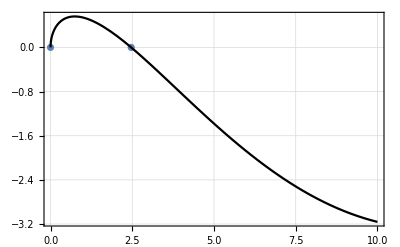

```mathematica
pv0=ListPlot[V0roots0Table];p0=Plot[TEQ0/.{ϵ->0},{v0,0,Vmax},PlotStyle->Black];Show[{pv0,p0},PlotRange->{{0,Vmax},All},Frame->True,GridLines->Automatic]
```

```mathematica
V0roots0[[2]]
```

2.4674

```mathematica
ϵ/.FindRoot[TEQ0/.v0->Vmax,{ϵ,-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2/.n->1}]
```

-4.62419

```mathematica
Vmax=1000;ListPlot[Table[{VV,ϵ/.FindRoot[TEQ0/.v0->VV,{ϵ,-VV+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,2.5,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

$Aborted

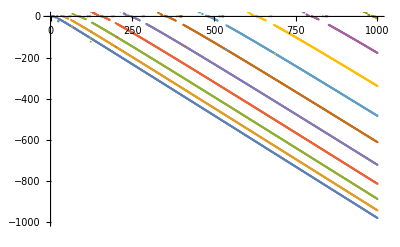

```mathematica
Vmax=1000;ListPlot[Table[{VV,ϵ/.FindRoot[TEQ1/.v0->VV,{ϵ,-VV+N[BesselJZero[3/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,3,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

Okay, there are some numerical quirks that need to be worked out here, and the code is clunky to be sure, but more or less this is right.